# Dynamic Models of Segregation (Schelling 1971)

```mathematica
ver110 (2016.1024thresholdの定義をムーア近傍内の同色ユニット割合に修正)
```

## 使い方

```mathematica
1.Module　セルを読み込む
2.評価->動的更新の実行にチェックを入れる
3.Manipulate　セルを読み込む
4.resetボタンを押す
5.run simulationのチェックボックスをon
6.終了すると END!! が出て自動的に停止する
7.条件を変えて4.から繰り返し
```

## Module

```mathematica
(*赤agent 青agentの初期配置*)
initialset[size_,redn_,bluen_]:=
Module[{a,b,n=redn+bluen},
Developer`ToPackedArray[(* Integer型指定で高速化 *)
a=RandomSample[Range[size*size],n];(* 総エージェント数だけ1次元配列から非復元抽出 *)
b=Flatten[Table[{i,j},{i,1,size},{j,1,size}],1];(* 2次元座標 *)
(* 抽出した1次元配列番号を座標に変換する．　前半は赤，後半は青用 *)
{Table[b⟦a⟦i⟧⟧,{i,1,redn}],Table[b⟦a⟦i⟧⟧,{i,redn+1,n}]},Integer]
];
(* 非復元抽出で初期配置を与える．
output: {{赤の位置情報}，{青の位置情報}} の順で出力する
initialset[size,redn,bluen]⟦1⟧ 赤初期配置　　initialset[size,redn,bluen]⟦2⟧　青初期配置　　*)

(*初期グリッド*)
zerogrid[size_]:=Table[0,{size},{size}]

(*  agentの位置情報を検索して，可視化する関数 *)
visualize[{redposi_,blueposi_},size_]:=Module[{zero1=zerogrid[size](*Mnipulate内で指定*)},
(* Embedding agents into zero1 for visualization 
引数のredposi_,blueposi_はそれぞれ「赤」と「青」の現在位置　*)
Do[zero1⟦ Sequence@@redposi⟦i,{1,2}⟧⟧=1,{i,Length[redposi]}];
Do[zero1⟦ Sequence@@blueposi⟦i,{1,2}⟧⟧=2,{i,Length[blueposi]}];
ArrayPlot[zero1,ColorFunction->(If[#==0,White,If[#==1,Darker[Red],Darker[Blue]]]&),
ColorFunctionScaling->False,ImageSize->{300,300},AspectRatio->Automatic,Frame->False,Mesh->All,Axes->False]
];

(* トーラス上に配置されたエゴのムーア近傍を出力する関数 *)
moore[t_(* agent's position *),size_]:=Module[{m=size,p1,p2,p3,p6,p4,p7,p8,p9,network},
p6=Table[If[t⟦i⟧⟦2⟧!=m,t⟦i⟧+{0,1},t⟦i⟧+{0,-(m-1)}],{i,Length[t]}];
p9=Table[Which[(*　+-している1を一般化すれば近傍の距離を自由に定義できる*)
(t⟦i⟧⟦1⟧!=1)&&(t⟦i⟧⟦2⟧!=m),t⟦i⟧+{-1,1},
(t⟦i⟧⟦1⟧==1)&&(t⟦i⟧⟦2⟧==m),t⟦i⟧+{m-1,-(m-1)},
(t⟦i⟧⟦1⟧==1)&&(t⟦i⟧⟦2⟧!=m),t⟦i⟧+{m-1,1},
(t⟦i⟧⟦1⟧!=1)&&(t⟦i⟧⟦2⟧==m),t⟦i⟧+{-1,-(m-1)}],{i,Length[t]}];
p7=Table[Which[
(t⟦i⟧⟦1⟧!=1)&&(t⟦i⟧⟦2⟧≠1),t⟦i⟧+{-1,-1},
(t⟦i⟧⟦1⟧==1)&&(t⟦i⟧⟦2⟧==1),t⟦i⟧+{m-1,(m-1)},
(t⟦i⟧⟦1⟧==1)&&(t⟦i⟧⟦2⟧≠1),t⟦i⟧+{m-1,-1},
(t⟦i⟧⟦1⟧!=1)&&(t⟦i⟧⟦2⟧==1),t⟦i⟧+{-1,(m-1)}],{i,Length[t]}];
p3=Table[Which[
(t⟦i⟧⟦1⟧≠m)&&(t⟦i⟧⟦2⟧!=m),t⟦i⟧+{1,1},
(t⟦i⟧⟦1⟧==m)&&(t⟦i⟧⟦2⟧==m),t⟦i⟧+{-(m-1),-(m-1)},
(t⟦i⟧⟦1⟧==m)&&(t⟦i⟧⟦2⟧!=m),t⟦i⟧+{-(m-1),1},
(t⟦i⟧⟦1⟧≠m)&&(t⟦i⟧⟦2⟧==m),t⟦i⟧+{1,-(m-1)}],{i,Length[t]}];
p1=Table[Which[
(t⟦i⟧⟦1⟧≠m)&&(t⟦i⟧⟦2⟧≠1),t⟦i⟧+{1,-1},
(t⟦i⟧⟦1⟧==m)&&(t⟦i⟧⟦2⟧==1),t⟦i⟧+{-(m-1),(m-1)},
(t⟦i⟧⟦1⟧==m)&&(t⟦i⟧⟦2⟧≠1),t⟦i⟧+{-(m-1),-1},
(t⟦i⟧⟦1⟧≠m)&&(t⟦i⟧⟦2⟧==1),t⟦i⟧+{1,(m-1)}],{i,Length[t]}];
p4=Table[If[t⟦i⟧⟦2⟧!=1,t⟦i⟧+{0,-1},t⟦i⟧+{0,(m-1)}],{i,Length[t]}];
p2=Table[If[t⟦i⟧⟦1⟧≠m,t⟦i⟧+{1,0},t⟦i⟧+{-(m-1),0}],{i,Length[t]}];
p8=Table[If[t⟦i⟧⟦1⟧≠1,t⟦i⟧+{-1,0},t⟦i⟧+{(m-1),0}],{i,Length[t]}];
network=Developer`ToPackedArray[
Table[{p6⟦i⟧,p4⟦i⟧,p2⟦i⟧,p8⟦i⟧,p9⟦i⟧,p7⟦i⟧,p3⟦i⟧,p1⟦i⟧},{i,Length[t]}],Integer]
];

(*　ムーア近傍情報に基づき幸福度（ムーア近傍内の同色エージェント割合）を計算,　位置情報に幸福度を追加　　
引数 agentposiは単色エージェント　*)
happy[agentposi_,size_]:=Module[{neloca,happy3},
neloca=moore[agentposi,size];
happy3=Table[Plus@@Table[If[MemberQ[agentposi,neloca⟦i⟧⟦j⟧],1,0],{j,8}],
{i,1,Length[neloca]}];
happy3=happy3/8;(* 同色エージェント数を *)
Table[Append[agentposi⟦i⟧,happy3⟦i⟧],{i,Length[agentposi]}]
];

(*入力は  {{1,1},{2,1},{3,1}}　のような単色エージェントの位置情報．出力は
{{1,1,0.2},{2,1,0.3},{3,1,0.8}}
のような　位置情報+幸福度
*)


(* 幸福情報に基づき，移動する　visualizeの引数を生成する *)
move[agents_,size_,redth_,blueth_,movern_]:=Module[{preloca,zerolocate,red0,blue0,red1,blue1,k1,k2,AllocationforRed,l1,l2,AllocationforBlue},
red0=agents⟦1⟧;blue0=agents⟦2⟧;
red1=happy[red0,size];blue1=happy[blue0,size];
preloca=Flatten[{red0,blue0},1];(* 埋まっているセル *)
zerolocate=Complement[Tuples[Range[size],2],preloca];(*ゼロセルの番地リスト*)

(*red agentからmovern人を選び動かす*非復元抽出* *)
k1=RandomSample[Range[Length[red0]],movern];
k2=Select[k1,red1⟦#,3⟧<redth&];
AllocationforRed=RandomSample[zerolocate,Length[k2]];
red⟦k2⟧=AllocationforRed;

(*Blue agentからmovern人を選び動かす*非復元抽出* *)
l1=RandomSample[Range[Length[blue0]],movern];
l2=Select[l1,blue1⟦#,3⟧<blueth&];
AllocationforBlue=RandomSample[Complement[zerolocate,AllocationforRed],Length[l2]];
blue⟦l2⟧=AllocationforBlue;

{red,blue}

];
```

## Manipulate

```mathematica
(*  ver090:自動停止機能を追加，happy level モニタリングをDynamic追加 *)
Manipulate[
Refresh[
If[moving,{red,blue}=move[{red,blue},s,redth,blueth,nomove]](* 更新している部分 *);
If[(Min[happy[red,s]⟦All,3⟧]>=redth)&&(Min[happy[blue,s]⟦All,3⟧]≥blueth),moving=False;
state=Text[Style["END !",Red,20]],moving=moving];
state2=Mean[happy[red,s]⟦All,3⟧]//N;
state3=Mean[happy[blue,s]⟦All,3⟧]//N;
(*  agent's happy を 監視して，全員が満足したらmoving をFalseに切り替え,Dynamic[state]表示をendに変える．
moving の値がFalseになると　{red,blue}の更新が終わり，"run simulation"チェックボックスがoffになる*)
visualize[{red,blue},s],UpdateInterval->If[moving,0,Infinity]](* reflesh end *),

(* 以下スライダ領域の指定　 *)
{{s,20,"length of a side"},10,30,1,ImageSize->Tiny,Appearance->"Labeled"},
{{redn,Floor[2*s],"number of red"},1,Floor[(s*s)/2],1,ImageSize->Tiny,Appearance->"Labeled"},
{{bluen,Floor[2*s],"number of blue"},1,Floor[(s*s)/2],1,ImageSize->Tiny,Appearance->"Labeled"},
{{redth,0.35,"red threshold"},0,1,ImageSize->Tiny,Appearance->"Labeled"},
{{blueth,0.35,"blue threshold"},0,1,ImageSize->Tiny,Appearance->"Labeled"},{{nomove,Floor[(s)/5],"number of mover"},1,Min[{redn,bluen}],1,ImageSize->Tiny,Appearance->"Labeled"},
{{moving,False,"run simulation"},{True, False}},
Button["reset",moving=False;state="going...";x=initialset[s,redn,bluen];red=x⟦1⟧;blue=x⟦2⟧,
ImageSize->Medium],
Dynamic[{"state=",state}],
Dynamic[{"red's mean happy= ",state2}],
Dynamic[{"blue's mean happy= ",state3}],
SaveDefinitions->True,TrackedSymbols:>{moving,red,blue,redn,bluen,s},
SynchronousUpdating->True,ControlPlacement->Left
]
```

```mathematica
(* length of a side の値を減らすとエラーが出るが，resetを押せば問題ない 
initialsetが実行されるまで，dynamicが 前の値を参照するせい*)
```

## Manipulate 2

```mathematica
幸福度をグラフでリアルタイムに更新
```

```mathematica
(*  ver110:幸福度をlistplotでリアルタイムに更新
自動停止機能を追加，happy level モニタリングをDynamic追加 *)
Manipulate[
Refresh[
If[moving,{red,blue}=move[{red,blue},s,redth,blueth,nomove]](* 更新している部分 *);
If[(Min[happy[red,s]⟦All,3⟧]>=redth)&&(Min[happy[blue,s]⟦All,3⟧]≥blueth),moving=False;
state=Text[Style["END !",Red,20]],moving=moving];
state2=Mean[happy[red,s]⟦All,3⟧]//N;
state3=Mean[happy[blue,s]⟦All,3⟧]//N;
(*  agent's happy を 監視して，全員が満足したらmoving をFalseに切り替え,Dynamic[state]表示をendに変える．
moving の値がFalseになると　{red,blue}の更新が終わり，"run simulation"チェックボックスがoffになる*)
visualize[{red,blue},s],UpdateInterval->If[moving,0.01,Infinity]](* reflesh end *),

{{s,20,"length of a side"},10,30,1,ImageSize->Tiny,Appearance->"Labeled"},
{{redn,Floor[2*s],"number of red"},1,Floor[(s*s)/2],1,ImageSize->Tiny,Appearance->"Labeled"},
{{bluen,Floor[2*s],"number of blue"},1,Floor[(s*s)/2],1,ImageSize->Tiny,Appearance->"Labeled"},
{{redth,0.35,"red threshold"},0,1,ImageSize->Tiny,Appearance->"Labeled"},
{{blueth,0.35,"blue threshold"},0,1,ImageSize->Tiny,Appearance->"Labeled"},{{nomove,Floor[(s)/5],"number of mover"},1,Min[{redn,bluen}],1,ImageSize->Tiny,Appearance->"Labeled"},
{{moving,False,"run simulation"},{True, False}},
Button["reset",moving=False;state="going...";x=initialset[s,redn,bluen];red=x⟦1⟧;blue=x⟦2⟧,
ImageSize->Medium],
Dynamic[{"state=",state}],
Dynamic[ListPlot[{{{1,state2}},{{2,state3}}},Filling->Axis,PlotRange->{{0,3},{0,1}},PlotMarkers->{Red,Blue}]],
SaveDefinitions->True,TrackedSymbols:>{moving,red,blue,redn,bluen,s},
SynchronousUpdating->True,ControlPlacement->Left
]
```

## initialset[ ], visualize[ ]の使用例

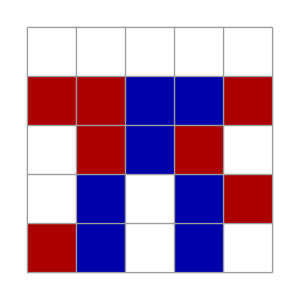

```mathematica
Module[{size=5,posi},
posi=initialset[size(*size*),7(*redn*),7(*bluen*)];
visualize[posi,size]
]
```

{{1,4,3/8},{5,5,1/4},{1,3,1/4},{5,3,1/2},{4,2,3/8},{4,3,1/4},{4,1,1/4}}

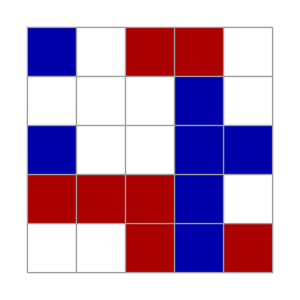

```mathematica
Module[{size=5,posi},
posi=initialset[size(*size*),7(*redn*),7(*bluen*)];
x=happy[posi⟦1⟧,size];
Print[x];
visualize[posi,size]
]
```